# PHSCS 230: Lab 10

## Carter Garrett

```mathematica
Clear["`*"]
```

## Assignment 1

### a)

```mathematica
a = 2b;
c= a + b;
d = b + c;
60 == d + a + b + c;
```

### b)

```mathematica
Clear[a,b,c,d]
Ages = {{-1, 2, 0 ,0}, {1,1,-1,0}, {0,1,1,-1},{1,1,1,1}};
Persons= {a,b,c,d};
Totals = {0,0,0,60};

LinearSolve[Ages, Totals]
```

{12,6,18,24}

## Assignment 2

### a)

```mathematica
M = {{1,2,3}, {3,1,2}, {2,3,1}};
%//MatrixForm
Apply[Plus, Diagonal[M] ]
Tr[M]
%==Apply[Plus, Diagonal[M] ]
```

(1 | 2 | 3
3 | 1 | 2
2 | 3 | 1)

3

3

True

### b)

```mathematica
Det[M]
Det[Inverse[M]]
```

18

1/18

The determinant of the inverse is the inverse of the value produced by the determinant.

### c)

```mathematica
det0m = {{1,1,1},{2,2,2},{0,0,0}};
Det[det0m]
Det[Inverse[det0m]]
(*it doesn't work*)
```

0

Inverse::sing: Matrix {{1,1,1},{2,2,2},{0,0,0}} is singular.

Det[Inverse[{{1,1,1},{2,2,2},{0,0,0}}]]

## Assignment 3

λ(u_0
v_0) = (k_b+k_s | -k_s
-k_s | k_b+k_s)(u_0
v_0)

### a)

```mathematica
m = 1; Subscript[k, s] = Subscript[k, b] = 1;
kmatrix= {{Subscript[k, s] + Subscript[k, b] , -Subscript[k, s]}, {-Subscript[k, s], Subscript[k, b] + Subscript[k, s]}};
eigenvalues3 = Eigenvalues[kmatrix]
Eigenvectors[kmatrix]

ω[ev_] := √(ev/m);
{ω[eigenvalues3[[1]]], ω[eigenvalues3[[2]]]}
(*FREQ FOR UNCOUPLED AND QUALITATIVE EXPLANATION*)
```

{3,1}

{{-1,1},{1,1}}

{√3,1}

The first eigenvalue gives a frequency that is much higher than the second. The first case describes the instance where the masses are moving in opposite directions, because when the masses are opposed, we see a force from the spring in the middle bringing them together, and a force from both outer springs, also pushing the masses together. In the other case, the masses move normally, at a lower frequency.

## Assignment 4

```mathematica
Clear[m,kb,ks,u,v,M] (* in case these variables were set to values above *)
M = {{kb+ks,-ks},{-ks,kb+ks}};  (* the matrix of spring constants *)
unknowns ={u[t],v[t]};    (* This is the vector x, containing u(t) and v(t) *)
equations = (#==0&)/@ (m D[unknowns,{t,2}]+M.unknowns);
initialconditions = {u[0]==u0,u'[0]==uvel0,v[0]==v0,v'[0]==vvel0};  (* u0 and uvel0 are initial position and velocity for mass 1; v0 and vvel0 are same thing for mass 2 *)
positions = unknowns/.DSolve[{equations,initialconditions},unknowns,t][[1]];
```

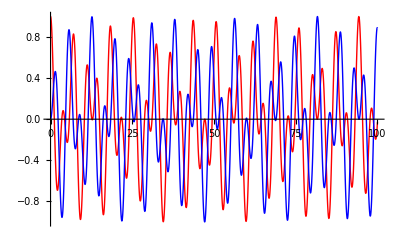

```mathematica
timedep = positions /.{m->1,kb->1,ks->1,u0->1, v0->0,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

### a)

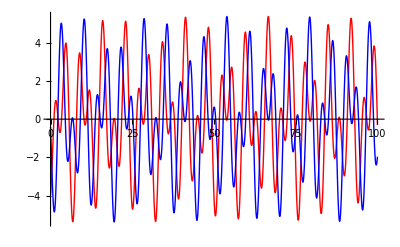

```mathematica
timedep = positions/.{m->1,kb->1,ks->1,u0->-4, v0->-0.4,uvel0->2,vvel0->-5}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

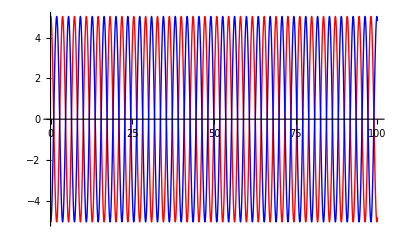

```mathematica
timedep = positions/.{m->1,kb->1,ks->1,u0->5, v0->-5,uvel0->1,vvel0->-1}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

The case requested:

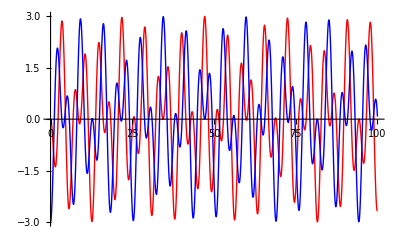

```mathematica
timedep = positions/.{m->1,kb->1,ks->1,u0->0, v0->-3,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

### b)

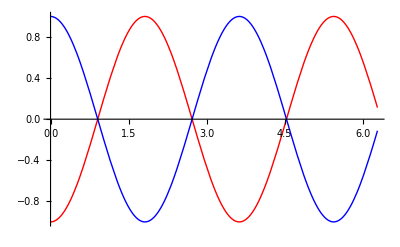

√3

3.6276

```mathematica
timedep = positions/.{m->1,kb->1,ks->1,u0->-1, v0->1,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,2π},PlotStyle->{{Thick,Red},{Thick,Blue}}]
ω3 = ω[eigenvalues3[[1]]]
(2π)/ω3 //N
```

We observe the same period as when we calculate the period from our eigenvalues.

### c)

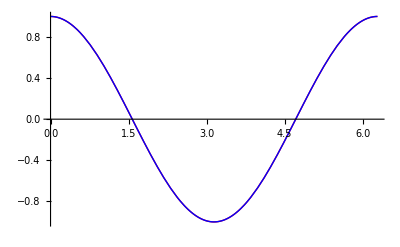

2 π

```mathematica
timedep = positions/.{m->1,kb->1,ks->1,u0->1, v0->1,uvel0->0,vvel0->0}//Re//ComplexExpand//Chop;
Plot[timedep,{t,0,2π},PlotStyle->{{Thick,Red},{Thick,Blue}}]

ω4 = ω[eigenvalues3[[2]]];
2π/ω4
```

A full period observed occurs in the same duration.

## Assignment 5

### a)

```mathematica
v= {4,-4};
Rotation= 90 Degree
lengthV = Norm[v] //N
R2d  = {{Cos[ϕ] , -Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}};
vnew = R2d.v /.ϕ->(Rotation) //N
lengthvnew= Norm[vnew] //N
lengthV == lengthvnew
```

90 °

5.65685

{4.,4.}

5.65685

True

### b)

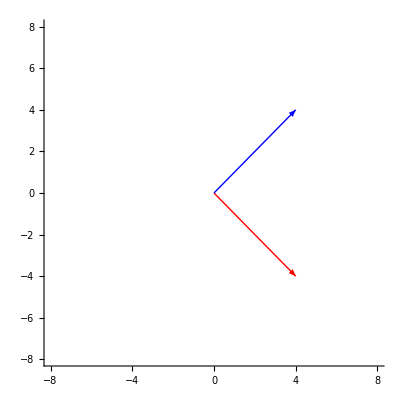

```mathematica
Graphics[{Red, Arrow[{{0,0}, v}],Blue, Arrow[{{0,0}, vnew}]}, Axes->True, AspectRatio->1, PlotRange->{{-8,8}, {-8,8}}]


(*arrowRotate =Arrow[ vnew/.ϕ->Rotation//N]
Graphics[{arrowPrior,arrowRotate}]*)
```

### c)

```mathematica
res1 = ArcTan[v[[2]]/v[[1]]] 
res2 = ArcTan[vnew[[2]]/vnew[[1]]]
(Abs[res1] + Abs[res2])*180/π
```

-π/4

0.785398

90.

### d)

```mathematica
Simplify[Det[R2d]]
Print["✓"]
```

1

✓

```mathematica
Simplify[Inverse[R2d] == Transpose[R2d]]
Print["✓"]
```

True

✓

## Assignment 6

### a)

```mathematica
M1 = {{7,2,3},{2,6,2},{3,2,1}} ;
S = RandomInteger[{-10,10}, {3,3}];
M2 = Inverse[S].M1.S
```

{{937/809,2965/809,-155/809},{196/809,2998/809,1052/809},{-6067/809,5229/809,7391/809}}

### b)

```mathematica
Tr[M1]
Tr[M2]
Tr[M1] == Tr[M2]
```

14

14

True

### c)

```mathematica
Det[M1]
Det[M2]
Det[M1] == Det[M2]
```

-20

-20

True

### d)

```mathematica
Eigenvalues[M1]
Eigenvalues[M2]
Eigenvalues[M1]==Eigenvalues[M2]
```

{10,2+√6,2-√6}

{10,2+√6,2-√6}

True

#### e)

```mathematica
Eigenvectors[M1]
Eigenvectors[M2]
Eigenvectors[M1] == Eigenvectors[M2]
```

{{4,3,2},{-(2+3 √6)/(-8+3 √6),(2 (4+√6))/(-8+3 √6),1},{-(-2+3 √6)/(8+3 √6),(2 (-4+√6))/(8+3 √6),1}}

{{60/923,193/923,1},{-(7902-7153 √6)/(-11616+6067 √6),-(4 (-2322+49 √6))/(-11616+6067 √6),1},{-(-7902-7153 √6)/(11616+6067 √6),-(4 (2322+49 √6))/(11616+6067 √6),1}}

False

## Assignment 7

```mathematica
Clear["M"]
M = RandomReal[{-10,10},{3,3}];
% //MatrixForm
```

(9.42235 | 7.87544 | 4.44166
-6.54327 | 1.58545 | 7.41529
7.5003 | -0.737002 | -5.07971)

### a)

```mathematica
egM  =Eigenvalues[M]
DiagonalMatrix[egM]
```

{9.22061+0. ⅈ,-1.64626+3.2177 ⅈ,-1.64626-3.2177 ⅈ}

{{9.22061+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.64626+3.2177 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-1.64626-3.2177 ⅈ}}

### b)

```mathematica
Clear["S"]
eigVM = Transpose[Eigenvectors[M]];
DiagM = Chop[Inverse[eigVM].M.eigVM]
MatrixForm[%]
```

{{9.22061,0,0},{0,-1.64626+3.2177 ⅈ,0},{0,0,-1.64626-3.2177 ⅈ}}

(9.22061 | 0 | 0
0 | -1.64626+3.2177 ⅈ | 0
0 | 0 | -1.64626-3.2177 ⅈ)

### c)

```mathematica
diagonalize[matrix_]:= Module[{newmatrix, S},
S = Transpose[Eigenvectors[matrix]];
newmatrix = Chop[Inverse[S].matrix.S];
MatrixForm[newmatrix]
]
diagonalize[M]
```

(9.22061 | 0 | 0
0 | -1.64626+3.2177 ⅈ | 0
0 | 0 | -1.64626-3.2177 ⅈ)

## Assignment 8

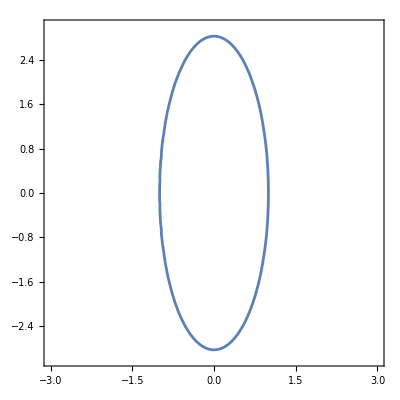

```mathematica
ContourPlot[x^2 + y^2/8==1, {x,-3,3}, {y,-3,3}]
```

#### b)

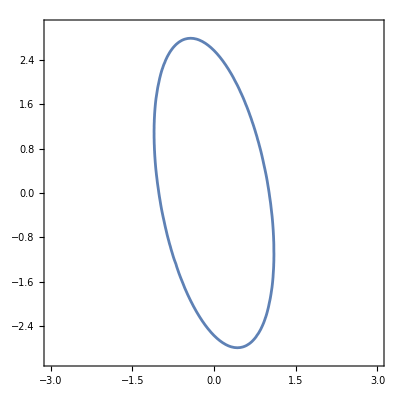

```mathematica
rmatrix = RotationMatrix[-10 Degree];
{NewX, NewY} =rmatrix.{x,y};
New1 = y^2/8/.y->NewY;
New2 = x^2/.x->NewX;
ContourPlot[New2 + New1 == 1, {x,-3,3}, {y,-3,3}]
```